```mathematica
(* This notebook contains almost all of the code required to reproduce the higher-spin results from https://doi.org/10.48550/arXiv.2512.14004

See Khadija's file uploads for the spin-9/2 Hamiltonian degeneracy plot in Fig. 8(e)  *)
```

```mathematica
ClearAll["Global`*"]
```

## Always run first: Spin operators and functions

```mathematica
I2 = IdentityMatrix[2]; Sx =1/2 PauliMatrix[1]; Sy =1/2 PauliMatrix[2]; Sz =1/2 PauliMatrix[3];

(* Nucleus *)
(* Khadija's code for producing operators of arbitrary spin *)
SpinX[S0_]:=Module[{S=S0},dim=2*S+1;m=Range[-S,S,1];mdash=Range[-S,S,1];el=ConstantArray[0,{dim,dim}];For[j=1,j<dim+1,j++,For[i=1,i<dim+1,i++,el[[i]][[j]]=(1/2)*(KroneckerDelta[mdash[[i]],m[[j]]+1]+KroneckerDelta[mdash[[i]]+1,m[[j]]])Sqrt[S(S+1)-mdash[[i]]m[[j]]]]];el]
SpinY[S0_]:=Module[{S=S0},dim=2*S+1;m=Range[-S,S,1];mdash=Range[-S,S,1];el=ConstantArray[0,{dim,dim}];For[j=1,j<dim+1,j++,For[i=1,i<dim+1,i++,el[[i]][[j]]=(1/2I)*(KroneckerDelta[mdash[[i]],m[[j]]+1]-KroneckerDelta[mdash[[i]]+1,m[[j]]])Sqrt[S(S+1)-mdash[[i]]m[[j]]]]];el]
SpinZ[S0_]:=Module[{S=S0},dim=2*S+1;m=Range[-S,S,1];mdash=Range[-S,S,1];el=ConstantArray[0,{dim,dim}];For[j=1,j<dim+1,j++,For[i=1,i<dim+1,i++,el[[i]][[j]]=KroneckerDelta[mdash[[i]],m[[j]]]m[[j]]]];el];

CircleTimes[A_,B_] := KroneckerProduct[A,B];
Commute[A_,B_] := A.B - B.A;

(* Define higher spin nuclear operators *)
Iz = SpinZ[9/2];
Ix = SpinX[9/2];
Iy = SpinY[9/2];
```

## Fig. 7

### Calculate free evolution one-tangling power for single nucleus

```mathematica
(* free evolution single nuclear one-tangling power for numerical approach *)
(* CPMG nuclear one-tangling power *)
nuclearonetanglefree[ωn1_, a_, Dq_, anc1_, θ1_,tvals_]:= Module[{M1, M2, M1List,  M2List, R0free,R0freedag,  R1free, R1freedag,  G1freept1, G1freept2, TrG1freept1, TrG1freept2, d, G1free}, 

(* Setting up matrices that will form rotation operators *)
M1[t_]:=(ωn1 Iz +1/2 a Iz +Dq Iz.Iz -anc1/2 ((Cos[θ1])^2 (Ix.Ix-Iy.Iy)-Sin[2 θ1] (Iz.Ix+Ix.Iz)))t;
M2[t_]:=(ωn1 Iz -1/2 a Iz +Dq Iz.Iz +anc1/2 ((Cos[θ1])^2 (Ix.Ix-Iy.Iy)-Sin[2 θ1] (Iz.Ix+Ix.Iz))) t;

(* Generate all possible values over time *)
M1List = ParallelTable[M1[t],{t,tvals}];
M2List = ParallelTable[M2[t],{t,tvals}];

(* Form free evolution rotation operators *)
R0free=Map[MatrixExp[-I*#]&,M1List];
R1free=Map[MatrixExp[-I*#]&,M2List];

R0freedag=Map[MatrixExp[I*#]&,M1List];
R1freedag=Map[MatrixExp[I*#]&,M2List];

(* Build up G1 in parts *)
G1freept1 = MapThread[#1.#2&,{R0free,R1freedag}];
G1freept2 = MapThread[#1.#2&,{R0freedag,R1free}];

TrG1freept1 = Map[Tr,G1freept1];
TrG1freept2 = Map[Tr,G1freept2];

d = 10;
G1free = 1/d^2 TrG1freept1*TrG1freept2;

1/3(d/(d+1))(1 - G1free)//Chop

]
```

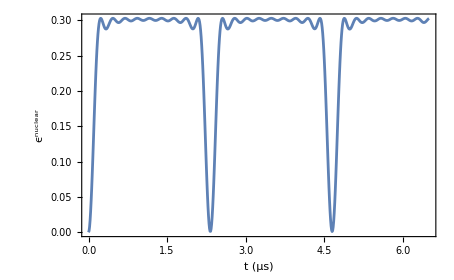
```mathematica
(* One-tangling power with respect to a single spin-9/2 nucleus interacting with a freely evolving electron *)

(* parameters used in MHz where applicable *)
a1 = 0.43*2π;
ωn1 = 9.33*2π;
Dq1 = 2π*0.058;
anc1 = 2π*0.034;

θ1 = π/3;

(* time in μs *)
tstart = 0;
tend = 6.5;
tstep = 0.01;
tvals = ParallelTable[t,{t,tstart,tend,tstep}];

Spinninehalffreeotp = nuclearonetanglefree[ωn1, a1, Dq1, anc1, θ1, tvals];
(* Fig. 1(a): Free evolution nuclear one-tangling power *)
ListPlot[{Transpose[{tvals,Spinninehalffreeotp}]},Joined-> True, Frame-> True,FrameLabel->{"t (μs)","ϵ^nuclear"}, LabelStyle->{Directive[Black],30}, FrameStyle->Directive[Black], PlotRange-> All]
-Graphics-
```

## Fig. 8(a)

```mathematica
(* To save on memory I split the results for Fig. 8(a) into quarters and stitched them together at the end *)
```

### Parameter distributions

```mathematica
(* First solve for the density of spins per area in the dot *)
NN = 80000;
R = 25; (* nm *)

ρ = NN/(π R^2);

rstart = 0;
rend = 25;
rstep = 0.056;

rvals = ParallelTable[r,{r,rstart,rend,rstep}]//Flatten;

(* The number of nuclei at a given annulus in the dot is given by  *)
nn[r_] := ρ 2 π r (rstep);
nnvals = Table[nn[r],{r,rstart,rend,rstep}]//Flatten;

(* We now have to compute the number of nuclei that have a particular hf and quadrupolar coupling strength value *)
hfvalsfunc[x_] := -2π*15.49*PDF[NormalDistribution[0, 7], x];
avals = ParallelTable[hfvalsfunc[r],{r,rstart,rend,rstep}];

θ1 = π/3;
qvalsfunc[x_] := 2π*0.521*PDF[NormalDistribution[0,7],x];
qvals = ParallelTable[qvalsfunc[r],{r,rstart,rend,rstep}];
qvals = qvals(Sin[θ1]^2 - 1/2 Cos[θ1]^2);

(* For a given position r we have a hf coupling parameter corresponding to it. The number of nuclei located at this position r will dictate the number of times we include that given hf coupling value *)
avalscount = {};
For[i = 1, i<= Length[rvals], i++, AppendTo[avalscount, ConstantArray[avals[[i]],Ceiling[nnvals[[i]]]]]];
avalscount = avalscount//Flatten;

qvalscount = {};
For[i = 1, i<= Length[rvals], i++, AppendTo[qvalscount, ConstantArray[qvals[[i]],Ceiling[nnvals[[i]]]]]];
qvalscount = qvalscount//Flatten;

(* counts of radial positions based on how many nuclei have this radius *)
rcounts = {};
For[i=1,i<= Length[rvals],i++,AppendTo[rcounts,ConstantArray[rvals[[i]],Ceiling[nnvals[[i]]]]]];
rcounts = rcounts//Flatten;


(* this is where the parameter values are split into chunks to generate each section of the plot *)
avalscountfirstquarter = Take[avalscount,Floor[Length[avalscount]/4]];
qvalscountfirstquarter = Take[qvalscount,Floor[Length[qvalscount]/4]];
rcountsfirstquarter = Take[rcounts,Floor[Length[rcounts]/4]];

avalscountsecondquarter = Take[avalscount,{Floor[Length[avalscount]/4]+1,Floor[Length[avalscount]/2]}];
qvalscountsecondquarter = Take[qvalscount,{Floor[Length[qvalscount]/4]+1, Floor[Length[avalscount]/2]}];
rcountssecondquarter = Take[rcounts,{Floor[Length[rcounts]/4]+1, Floor[Length[avalscount]/2]}];

avalscountthirdquarter = Take[avalscount,{Floor[Length[avalscount]/2]+1,Floor[3*Length[avalscount]/4]}];
qvalscountthirdquarter = Take[qvalscount,{Floor[Length[qvalscount]/2]+1, Floor[3*Length[avalscount]/4]}];
rcountsthirdquarter = Take[rcounts,{Floor[Length[rcounts]/2]+1, Floor[3*Length[avalscount]/4]}];

avalscountfourthquarter = Take[avalscount,{Floor[3*Length[avalscount]/4]+1,Length[avalscount]}];
qvalscountfourthquarter = Take[qvalscount,{Floor[3*Length[qvalscount]/4]+1, Length[avalscount]}];
rcountsfourthquarter = Take[rcounts,{Floor[3*Length[rcounts]/4]+1, Length[avalscount]}];

(* Checking that the total length matches the size of the bath from the main text *)
Join[avalscountfirstquarter,avalscountsecondquarter,avalscountthirdquarter,avalscountfourthquarter]//Length
```

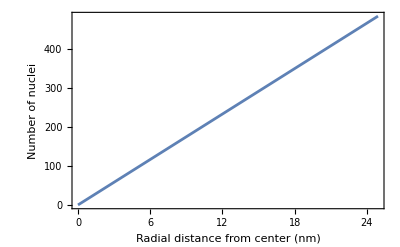

```mathematica
ListPlot[Transpose@{rvals,nnvals},PlotRange->All,Joined-> True, Frame-> True, FrameStyle->Directive[Black, 20], FrameLabel->{"Radial distance from center (nm)","Number of nuclei"}]
```

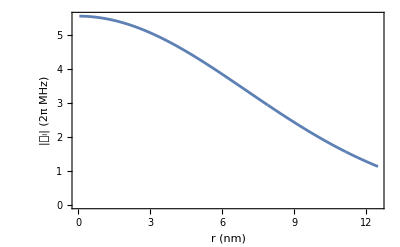

```mathematica
ListPlot[Transpose@{rcountsfirstquarter,Abs[avalscountfirstquarter]},PlotRange->All,Joined-> True, Frame-> True, FrameStyle->Directive[Black, 20], FrameLabel->{"r (nm)","|(|01d44e)_i| (2π MHz)"}]
```

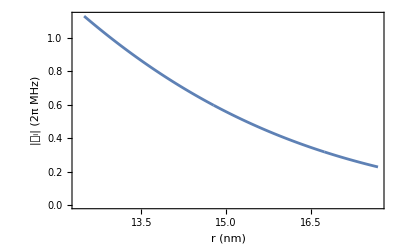

```mathematica
ListPlot[Transpose@{rcountssecondquarter,Abs[avalscountsecondquarter]},PlotRange->All,Joined-> True, Frame-> True, FrameStyle->Directive[Black, 20], FrameLabel->{"r (nm)","|(|01d44e)_i| (2π MHz)"}]
```

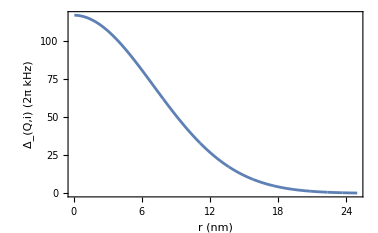

```mathematica
ListPlot[Transpose@{rcounts,qvalscount*1000},PlotRange->All,Joined-> True, Frame-> True, FrameStyle->Directive[Black, 20], FrameLabel->{"r (nm)","Δ_(Q,i) (2π kHz)"}]
```

### Nuclear one-tangling power: free evolution for distribution of 80,000 nuclei, analytical and numerical for counts of nuclei

```mathematica
epsilonnuc[avalscountgroup_, qvalscountgroup_,rcountsgroup_]:= Module[{Ix, Iy, Iz, anc1, ωn1, θ1, d, M0,M1,M0list,M1list, R0, R0dag, R1, R1dag, G1pt1,G1pt2, TrG1CPMGpt1,TrG1CPMGpt2, G1free, M1Listtest, M2Listtest, R0freetest, R1freetest, R0freetestdag, R1freetestdag, R0test, R1test, R0testdag, R1testdag, sepprod, NN, R, ρ, M2, G1test,G1testlist },

(* Spin operators and parameters *)
Ix = SpinX[9/2]; Iy = SpinY[9/2]; Iz = SpinZ[9/2];

θ1 = π/3;
anc1 = 2π*0.0051;
ωn1 = 2π*9.33;
d = Length[Iz];

(* Computing nuclear one-tangling power *)
M1[i_]:=ωn1 Iz+1/2 avalscountgroup[[i]] Iz+qvalscountgroup[[i]] Iz.Iz-anc1/2 ((Cos[θ1])^2 (Ix.Ix-Iy.Iy)-Sin[2 θ1] (Iz.Ix+Ix.Iz));
M2[i_]:=ωn1 Iz-1/2 avalscountgroup[[i]] Iz+qvalscountgroup[[i]] Iz.Iz+anc1/2 ((Cos[θ1])^2 (Ix.Ix-Iy.Iy)-Sin[2 θ1] (Iz.Ix+Ix.Iz));

M1Listtest = ParallelTable[M1[i],{i,Length[avalscountgroup]}];
M2Listtest = ParallelTable[M2[i],{i,Length[avalscountgroup]}];

R0freetest[t_] := Map[MatrixExp,-I M1Listtest t];
R1freetest[t_] := Map[MatrixExp,-I M2Listtest t];

R0freetestdag[t_] := Map[MatrixExp,I M1Listtest t];
R1freetestdag[t_] := Map[MatrixExp,I M2Listtest t];

R0test = R0freetest[t];
R1test = R1freetest[t];
R0testdag = R0freetestdag[t];
R1testdag = R1freetestdag[t];

G1test[i_] := 1/d^2 Tr[R0test[[i]].R1testdag[[i]]]*Tr[R0testdag[[i]].R1test[[i]]];
G1testlist = Map[G1test,Range[Length[avalscountgroup]]];

 1/3(d/(d+1))(1 - G1testlist)/. t-> 5.32

]
```

```mathematica
(**** For each desired section of the plot run one of these commented sections corresponding to one of the quarters of the parameter values from the distributions above and save the results ****)


(* epsilonnucfirstquarter = epsilonnuc[avalscountfirstquarter, qvalscountfirstquarter, rcountsfirstquarter]//Chop;
Export["/Users/ignosso/Desktop/epsilonspinninehalffirstquarterfullbath.mx",epsilonnucfirstquarter];
Export["/Users/ignosso/Desktop/rcountsspinninehalffirstquarterfullbath.mx",rcountsfirstquarter]; *)

(* epsilonnucsecondquarter = epsilonnuc[avalscountsecondquarter, qvalscountsecondquarter, rcountssecondquarter]//Chop;
Export["/Users/ignosso/Desktop/epsilonspinninehalfsecondquarterfullbath.mx",epsilonnucsecondquarter];
Export["/Users/ignosso/Desktop/rcountsspinninehalfsecondquarterfullbath.mx",rcountssecondquarter]; *)

(* epsilonnucthirdquarter = epsilonnuc[avalscountthirdquarter, qvalscountthirdquarter, rcountsthirdquarter]//Chop;
Export["/Users/ignosso/Desktop/epsilonspinninehalfthirdquarterfullbath.mx",epsilonnucthirdquarter];
Export["/Users/ignosso/Desktop/rcountsspinninehalfthirdquarterfullbath.mx",rcountsthirdquarter]; *)

epsilonnucfourthquarter = epsilonnuc[avalscountfourthquarter,qvalscountfourthquarter,rcountsfourthquarter]//Chop;
Export["/Users/ignosso/Desktop/epsilonspinninehalffourthquarterfullbath.mx",epsilonnucfourthquarter];
Export["/Users/ignosso/Desktop/rcountsspinninehalffourthquarterfullbath.mx",rcountsfourthquarter];
```

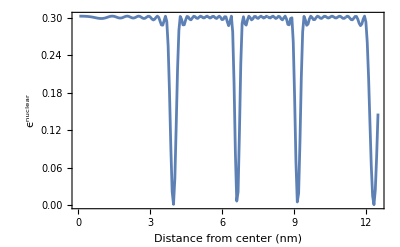

```mathematica
ListPlot[Transpose[{rcountsfirstquarter,epsilonnucfirstquarter}],Joined->True,Frame->True,FrameLabel->{"Distance from center (nm)","\!\(\*SuperscriptBox[\(ϵ\), \(nuclear\)]\)"},LabelStyle->{"Black",20},PlotRange->All,FrameStyle->Directive[Black,20]]
```

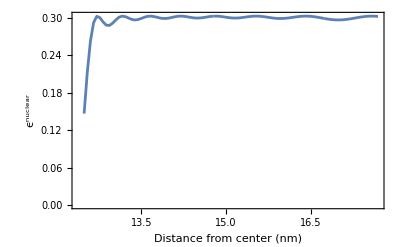

```mathematica
ListPlot[Transpose[{rcountssecondquarter,epsilonnucsecondquarter}],Joined->True,Frame->True,FrameLabel->{"Distance from center (nm)","\!\(\*SuperscriptBox[\(ϵ\), \(nuclear\)]\)"},LabelStyle->{"Black",20},PlotRange->All,FrameStyle->Directive[Black,20]]
```

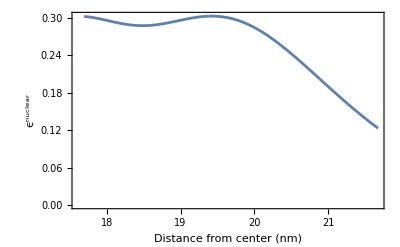

```mathematica
ListPlot[Transpose[{rcountsthirdquarter,epsilonnucthirdquarter}],Joined->True,Frame->True,FrameLabel->{"Distance from center (nm)","\!\(\*SuperscriptBox[\(ϵ\), \(nuclear\)]\)"},LabelStyle->{"Black",20},PlotRange->All,FrameStyle->Directive[Black,20]]
```

```mathematica
(* After clearing old data (or whatever memory allows) import data corresponding to all sections of the plot *)
epsilonnucfirstquarter = Import["/Users/ignosso/Desktop/epsilonvaluesspinninehalffirstquartertest.mx"];
epsilonnucsecondquarter = Import["/Users/ignosso/Desktop/epsilonvaluesspinninehalfsecondquartertest.mx"];
epsilonnucthirdquarter = Import["/Users/ignosso/Desktop/epsilonvaluesspinninehalfthirdquartertest.mx"];
epsilonnucfourthquarter = Import["/Users/ignosso/Desktop/epsilonvaluesspinninehalffourthquartertest.mx"];
```

```mathematica
(* Join each section *)
epsilonvals = Join[epsilonnucfirstquarter,epsilonnucsecondquarter, epsilonnucthirdquarter, epsilonnucfourthquarter];
rcountsnew = Join[rcountsfirstquarter, rcountssecondquarter, rcountsthirdquarter,rcountsfourthquarter];
```

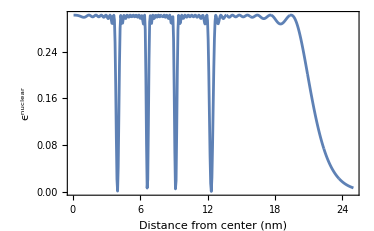

```mathematica
ListPlot[Transpose[{rcountsnew,epsilonvals}],Joined->True,Frame->True,FrameLabel->{"Distance from center (nm)","\!\(\*SuperscriptBox[\(ϵ\), \(nuclear\)]\)"},LabelStyle->{"Black",20},PlotRange->All,FrameStyle->Directive[Black,20]]
```

```mathematica
(* Need rcounts for x axis. This is a quicker way to generate the distribution that yields this result *)
rcounts := Module[{NN, R, ρ, rstart,rend, rstep, rvals, nn, nnvals, hfvalsfunc, avals, θ1, qvalsfunc, qvals, avalsfunc, avalscount,qvalscount },
NN = 80000;
R = 25; (* nm *)

ρ = NN/(π R^2);

rstart = 0;
rend = 25;
rstep = 0.056;(* 0.00031250390629882874;*) (* dr *)

rvals = ParallelTable[r,{r,rstart,rend,rstep}]//Flatten;

(* The number of nuclei at a given annulus in the dot is given by  *)
nn[r_] := ρ 2 π r (rstep);
nnvals = Table[nn[r],{r,rstart,rend,rstep}]//Flatten;


hfvalsfunc[x_] := -2π*15.49*PDF[NormalDistribution[0, 7], x];
avals = ParallelTable[hfvalsfunc[r],{r,rstart,rend,rstep}];

θ1 = π/3;
qvalsfunc[x_] := 2π*0.521*PDF[NormalDistribution[0,7],x];
qvals = ParallelTable[qvalsfunc[r],{r,rstart,rend,rstep}];
qvals = qvals(Sin[θ1]^2 - 1/2 Cos[θ1]^2);

avalscount = {};
For[i = 1, i<= Length[rvals], i++, AppendTo[avalscount, ConstantArray[avals[[i]],Ceiling[nnvals[[i]]]]]];
avalscount = avalscount//Flatten;

qvalscount = {};
For[i = 1, i<= Length[rvals], i++, AppendTo[qvalscount, ConstantArray[qvals[[i]],Ceiling[nnvals[[i]]]]]];
qvalscount = qvalscount//Flatten;

(* counts of radial positions based on how many nuclei have this radius *)
rcounts = {};
For[i=1,i<= Length[rvals],i++,AppendTo[rcounts,ConstantArray[rvals[[i]],Ceiling[nnvals[[i]]]]]];
rcounts = rcounts//Flatten

]
```

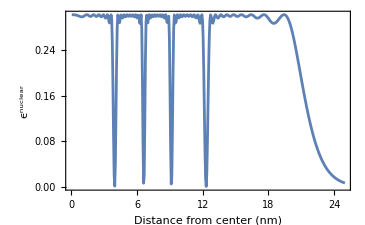

```mathematica
ListPlot[Transpose[{rcounts,epsilonnuc}],Joined->True,Frame->True,FrameLabel->{"Distance from center (nm)","\!\(\*SuperscriptBox[\(ϵ\), \(nuclear\)]\)"},LabelStyle->{"Black",20},PlotRange->All,FrameStyle->Directive[Black,20]]
```

## Fig. 8(b)

### Parameter Distributions

```mathematica
NN = 80000;
R = 25; (* nm *)

ρ = NN/(π R^2);

rstart = 0;
rend = 25;
rstep =0.056;
rvals = ParallelTable[r,{r,rstart,rend,rstep}]//Flatten;
(* The number of nuclei at a given annulus in the dot is given by  *)
nn[r_] := ρ 2 π r (rstep);
nnvals = Table[nn[r],{r,rstart,rend,rstep}]//Flatten;

(* We now have to compute the number of nuclei that have a particular hf and quadrupolar coupling strength value *)
hfvalsfunc[x_] := -2π*15.49*PDF[NormalDistribution[0, 7], x];
avals = ParallelTable[hfvalsfunc[r],{r,rstart,rend,rstep}];

qvalsfunc[x_] := 2π*0.521*PDF[NormalDistribution[0,7],x];
qvals = ParallelTable[qvalsfunc[r],{r,rstart,rend,rstep}];
qvals = qvals(Sin[θ1]^2 - 1/2 Cos[θ1]^2);

avalscount = {};
For[i = 1, i<= Length[rvals], i++, AppendTo[avalscount, ConstantArray[avals[[i]],Ceiling[nnvals[[i]]]]]];
avalscount = avalscount//Flatten;

qvalscount = {};
For[i = 1, i<= Length[rvals], i++, AppendTo[qvalscount, ConstantArray[qvals[[i]],Ceiling[nnvals[[i]]]]]];
qvalscount = qvalscount//Flatten;
```

### Spin operators and Larmor frequencies

```mathematica
(* Need a list of the nuclear spin operators-- whether they are spin-3/2 or 9/2 will change G1 *)
Izlist = {SpinZ[3/2],SpinZ[9/2]};
Ixlist = {SpinX[3/2],SpinX[9/2]};
Iylist = {SpinY[3/2],SpinY[9/2]};

(* The way this is setup right now means that avalscount has to be an even number *)
ωn1In = ConstantArray[2π*9.33, Floor[Length[avalscount]/2]];
ωn1Ga = ConstantArray[2π*12.98, Ceiling[Length[avalscount]/2]];
ωn1 = Join[ωn1In, ωn1Ga];

(* ωn1 = ResourceFunction["Shuffle"][ωn1,6]; *)
ωn1 = RandomSample[ωn1];

Ilistnumbers = {};
For[i = 1, i<= Length[ωn1], i++, If[ωn1[[i]]==2π*9.33, AppendTo[Ilistnumbers, 2], AppendTo[Ilistnumbers, 1]]];

Iz[i_] := Izlist[[Ilistnumbers[[i]]]];
Ix[i_]:= Ixlist[[Ilistnumbers[[i]]]];
Iy[i_]:= Iylist[[Ilistnumbers[[i]]]];
```

### Electronic one-tangling power

```mathematica
anc1 = 2π*0.0051;
θ1 = π/3;

M1[i_]:=ωn1[[i]] Iz[i]+1/2 avalscount[[i]] Iz[i]+qvalscount[[i]] Iz[i].Iz[i]-anc1/2 ((Cos[θ1])^2 (Ix[i].Ix[i]-Iy[i].Iy[i])-Sin[2 θ1] (Iz[i].Ix[i]+Ix[i].Iz[i]));

M2[i_]:=ωn1[[i]] Iz[i]-1/2 avalscount[[i]] Iz[i]+qvalscount[[i]] Iz[i].Iz[i]+anc1/2 ((Cos[θ1])^2 (Ix[i].Ix[i]-Iy[i].Iy[i])-Sin[2 θ1] (Iz[i].Ix[i]+Ix[i].Iz[i]));

M1Listtest = Table[M1[i],{i,Length[avalscount]}];
M2Listtest = Table[M2[i],{i,Length[avalscount]}];

R0freetest[t_] := Map[MatrixExp,-I M1Listtest t];
R1freetest[t_] := Map[MatrixExp,-I M2Listtest t];

R0freetestdag[t_] := Map[MatrixExp,I M1Listtest t];
R1freetestdag[t_] := Map[MatrixExp,I M2Listtest t];

G1freept1[t_] := MapThread[#1.#2&, {R0freetest[t],R1freetestdag[t]}];
G1freept2[t_] := MapThread[#1.#2&, {R0freetestdag[t],R1freetest[t]}];

TrG1freept1[t_] := Map[Tr,G1freept1[t]];
TrG1freept2[t_] := Map[Tr,G1freept2[t]];

dvals = {};
For[i = 1, i<= Length[ωn1],i++,
If[ωn1[[i]]==2π*12.98, AppendTo[dvals, 4], AppendTo[dvals,10]]
];

G1free[t_]:= 1/dvals^2 TrG1freept1[t]*TrG1freept2[t];
```

```mathematica
tstart = 0;
tend = 0.006;
tstep =0.000084;
tvals = ParallelTable[t,{t,tstart,tend,tstep}]//N;

prodsfree = {};
For[i = 1, i<= Length[tvals],i++, AppendTo[prodsfree, Fold[Times,1,(1/(dvals + 1))(1 + dvals G1free[tvals[[i]]])]]];

epsilonfree = 1/3-1/3 prodsfree;
```

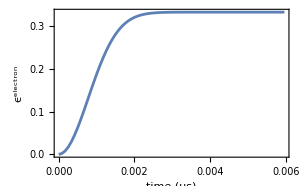

```mathematica
ListPlot[Transpose[{tvals,epsilonfree}],Joined->True,Frame->True,FrameLabel->{"time (μs)","\!\(\*SuperscriptBox[\(ϵ\), \(electron\)]\)"},LabelStyle->{"Black",15},PlotRange->All,FrameStyle->Directive[Black,15]]
```

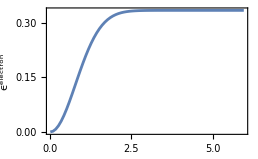

```mathematica
ListPlot[Transpose[{tvals*1000,epsilonfree}],Joined->True,Frame->True,FrameLabel->{"time (ns)","\!\(\*SuperscriptBox[\(ϵ\), \(electron\)]\)"},LabelStyle->{"Black",15},PlotRange->All,FrameStyle->Directive[Black,15]]
```

## Fig. 8(c)--same as (b) but now for CPMG evolution

### Distribution

```mathematica
NN = 80000;
R = 25; (* nm *)

ρ = NN/(π R^2);

rstart = 0;
rend = 25;
rstep =0.056;
rvals = ParallelTable[r,{r,rstart,rend,rstep}]//Flatten;
(* The number of nuclei at a given annulus in the dot is given by  *)
nn[r_] := ρ 2 π r (rstep);
nnvals = Table[nn[r],{r,rstart,rend,rstep}]//Flatten;

(* We now have to compute the number of nuclei that have a particular hf and quadrupolar coupling strength value *)
hfvalsfunc[x_] := -2π*15.49*PDF[NormalDistribution[0, 7], x];
avals = ParallelTable[hfvalsfunc[r],{r,rstart,rend,rstep}];

qvalsfunc[x_] := 2π*0.521*PDF[NormalDistribution[0,7],x];
qvals = ParallelTable[qvalsfunc[r],{r,rstart,rend,rstep}];
qvals = qvals(Sin[θ1]^2 - 1/2 Cos[θ1]^2);

avalscount = {};
For[i = 1, i<= Length[rvals], i++, AppendTo[avalscount, ConstantArray[avals[[i]],Ceiling[nnvals[[i]]]]]];
avalscount = avalscount//Flatten;

qvalscount = {};
For[i = 1, i<= Length[rvals], i++, AppendTo[qvalscount, ConstantArray[qvals[[i]],Ceiling[nnvals[[i]]]]]];
qvalscount = qvalscount//Flatten;
```

```mathematica
avalscount//Length
```

80247

### Spin operators and Larmor frequencies

```mathematica
(* Need a list of the nuclear spin operators-- whether they are spin-3/2 or 9/2 will change G1 *)
Izlist = {SpinZ[3/2],SpinZ[9/2]};
Ixlist = {SpinX[3/2],SpinX[9/2]};
Iylist = {SpinY[3/2],SpinY[9/2]};

(* The way this is setup right now means that avalscount has to be an even number *)
ωn1In = ConstantArray[2π*9.33, Floor[Length[avalscount]/2]];
ωn1Ga = ConstantArray[2π*12.98, Ceiling[Length[avalscount]/2]];
ωn1 = Join[ωn1In, ωn1Ga];

(* ωn1 = ResourceFunction["Shuffle"][ωn1,6]; *)
ωn1 = RandomSample[ωn1];

Ilistnumbers = {};
For[i = 1, i<= Length[ωn1], i++, If[ωn1[[i]]==2π*9.33, AppendTo[Ilistnumbers, 2], AppendTo[Ilistnumbers, 1]]];

Iz[i_] := Izlist[[Ilistnumbers[[i]]]];
Ix[i_]:= Ixlist[[Ilistnumbers[[i]]]];
Iy[i_]:= Iylist[[Ilistnumbers[[i]]]];
```

```mathematica
ωn1 //Length
```

80247

### Electronic one-tangling power

```mathematica
anc1 = 2π*0.0051;
θ1 = π/3;

M1[i_]:=ωn1[[i]] Iz[i]+1/2 avalscount[[i]] Iz[i]+qvalscount[[i]] Iz[i].Iz[i]-anc1/2 ((Cos[θ1])^2 (Ix[i].Ix[i]-Iy[i].Iy[i])-Sin[2 θ1] (Iz[i].Ix[i]+Ix[i].Iz[i]));

M2[i_]:=ωn1[[i]] Iz[i]-1/2 avalscount[[i]] Iz[i]+qvalscount[[i]] Iz[i].Iz[i]+anc1/2 ((Cos[θ1])^2 (Ix[i].Ix[i]-Iy[i].Iy[i])-Sin[2 θ1] (Iz[i].Ix[i]+Ix[i].Iz[i]));

M1Listtest = Table[M1[i],{i,Length[avalscount]}];
M2Listtest = Table[M2[i],{i,Length[avalscount]}];

R0freetest[t_] := Map[MatrixExp,-I M1Listtest t];
R1freetest[t_] := Map[MatrixExp,-I M2Listtest t];

R0freetestdag[t_] := Map[MatrixExp,I M1Listtest t];
R1freetestdag[t_] := Map[MatrixExp,I M2Listtest t];
```

```mathematica
R0testCPMG[t_] := MapThread[#1.#2.#1&, {R0freetest[t/4], R1freetest[t/2]}];
R1testCPMG[t_] := MapThread[#1.#2.#1&, {R1freetest[t/4], R0freetest[t/2]}];

R0testCPMGdag[t_]:= MapThread[#1.#2.#1&, {R0freetestdag[t/4], R1freetestdag[t/2]}];
R1testCPMGdag[t_]:= MapThread[#1.#2.#1&, {R1freetestdag[t/4], R0freetestdag[t/2]}];
```

```mathematica
G1CPMGpt1[t_] := MapThread[#1.#2&, {R0testCPMG[t],R1testCPMGdag[t]}];
G1CPMGpt2[t_] := MapThread[#1.#2&, {R0testCPMGdag[t],R1testCPMG[t]}];

TrG1CPMGpt1[t_] := Map[Tr,G1CPMGpt1[t]];
TrG1CPMGpt2[t_] := Map[Tr,G1CPMGpt2[t]];

dvals = {};
For[i = 1, i<= Length[ωn1],i++,
If[ωn1[[i]]==2π*12.98, AppendTo[dvals, 4], AppendTo[dvals,10]]
];

G1CPMG[t_]:= 1/dvals^2 TrG1CPMGpt1[t]*TrG1CPMGpt2[t];
```

```mathematica
(* tstart = 0;
tend = 0.006;
tstep =0.000084;
tvals = ParallelTable[t,{t,tstart,tend,tstep}]//N; *)
tstart = 0;
tend = 0.12;
tstep =0.00078;
tvals = ParallelTable[t,{t,tstart,tend,tstep}]//N;

prodsCPMG = {};
For[i = 1, i<= Length[tvals],i++, AppendTo[prodsCPMG, Fold[Times,1,(1/(dvals + 1))(1 + dvals G1CPMG[tvals[[i]]])]]];

epsilonCPMG = 1/3-1/3 prodsCPMG;
```

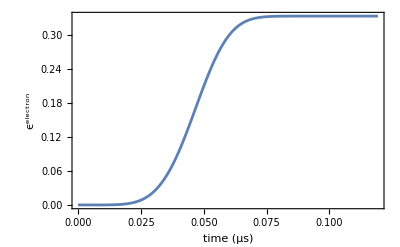

```mathematica
ListPlot[Transpose[{tvals,epsilonCPMG}],Joined->True,Frame->True,FrameLabel->{"time (μs)","\!\(\*SuperscriptBox[\(ϵ\), \(electron\)]\)"},LabelStyle->{"Black",15},PlotRange->All,FrameStyle->Directive[Black,15]]
```

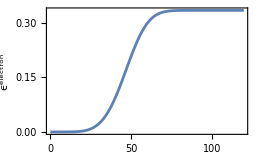

```mathematica
ListPlot[Transpose[{tvals*1000,epsilonCPMG}],Joined->True,Frame->True,FrameLabel->{"time (ns)","\!\(\*SuperscriptBox[\(ϵ\), \(electron\)]\)"},LabelStyle->{"Black",15},PlotRange->All,FrameStyle->Directive[Black,15]]
```

## Fig. 8(d)

```mathematica
(* I split this up into chunks saving the outputs for each section of the plot and then stitched them together with Join. Here I just show one section. Note that avals and Dqvals must always have the same dimension.  *)
```

```mathematica
ωn1 = 2.24*2π;
Dq1 = 2π*0.0024(* ωn1 *);
anc1 = 2π*0.0013 ;
θ1 = π/3;

astart = 0;
aend = 0.29*2π;
astep = 0.0077*2π;
avals = Table[a,{a,astart,aend,astep}];

Dqstart = 0;
Dqend = 0.29*2π ;
Dqstep =0.0077*2π ;
Dqvals = Table[Dq,{Dq,Dqstart,Dqend,Dqstep}];

tstart = 0;
tend = 35.6;
tstep = 0.053; 
tvals = Table[t,{t,tstart,tend,tstep}]//N; 

Iz = SpinZ[9/2];Ix = SpinX[9/2]; Iy = SpinY[9/2];

 (* Define H0, H1 matrices formed by plugging in all possible a, Dq values *)
M1[a_,Dq_,t_]:=(ωn1 Iz +1/2 a Iz +Dq Iz.Iz -anc1/2 ((Cos[θ1])^2 (Ix.Ix-Iy.Iy)-Sin[2 θ1] (Iz.Ix+Ix.Iz)))t;
M2[a_,Dq_,t_]:=(ωn1 Iz -1/2 a Iz+Dq Iz.Iz +anc1/2 ((Cos[θ1])^2 (Ix.Ix-Iy.Iy)-Sin[2 θ1] (Iz.Ix+Ix.Iz))) t;

M1List4 = ParallelTable[M1[i,j,t/4],{i,avals},{j,Dqvals},{t,tvals}];
M2List4 = ParallelTable[M2[i,j,t/4],{i,avals},{j,Dqvals},{t,tvals}];
M1List2 = ParallelTable[M1[i,j,t/2],{i,avals},{j,Dqvals},{t,tvals}];
M2List2 = ParallelTable[M2[i,j,t/2],{i,avals},{j,Dqvals},{t,tvals}];
```

{754.3,Null}

```mathematica
(* Form free evolution rotation *)
R04=Map[MatrixExp[-I*#]&,M1List4,{3}];
R14=Map[MatrixExp[-I*#]&,M2List4,{3}];

R0dag4=Map[MatrixExp[I*#]&,M1List4,{3}];
R1dag4=Map[MatrixExp[I*#]&,M2List4,{3}];

R02=Map[MatrixExp[-I*#]&,M1List2,{3}];
R12=Map[MatrixExp[-I*#]&,M2List2,{3}];

R0dag2=Map[MatrixExp[I*#]&,M1List2,{3}];
R1dag2=Map[MatrixExp[I*#]&,M2List2,{3}];

R0CPMG = MapThread[#1.#2.#3&, {R04,R12,R04},3];
R0CPMGdag = MapThread[#1.#2.#3&, {R0dag4,R1dag2,R0dag4},3];
R1CPMG = MapThread[#1.#2.#3&, {R14,R02,R14},3];
R1CPMGdag = MapThread[#1.#2.#3&,{R1dag4, R0dag2, R1dag4},3];

G1CPMGpt1 = MapThread[#1.#2&,{R0CPMG,R1CPMGdag},3];
G1CPMGpt2 = MapThread[#1.#2&,{R0CPMGdag,R1CPMG},3];

TrG1CPMGpt1 = Map[Tr,G1CPMGpt1, {3}];
TrG1CPMGpt2 = Map[Tr,G1CPMGpt2, {3}];
```

```mathematica
d = Length[Iz];

G1CPMG = 1/d^2 TrG1CPMGpt1*TrG1CPMGpt2;
ep = 1/3(d/(d+1))(1 - G1CPMG)//Chop;

maxvals=Apply[Max,ep,{2}];

xyzPairs1 = Table[Transpose@{avals[[j]]/ωn1,Dqvals[[k]]/ωn1,maxvals[[j]][[k]]},{j,1,Length[avals]},{k,1,Length[Dqvals]}];
xyzPairs1 = Flatten[xyzPairs1,1];
```

```mathematica
ListDensityPlot[xyzPairs1, PlotLegends-> True,PlotRange-> All , Frame->True,FrameLabel->{"a/ω_n","Δ/ω_n"},PlotLabel-> "Spin-9/2 ϵ^CPMG",LabelStyle-> {Directive[ Black],20}, MaxPlotPoints->200]
```

## See Khadija’s code for Fig. 8(e)

## Figs. 8(f)-(h)

```mathematica
a1 = 0.23*2π;
ωn1 = 9.33*2π;
Dq1 = 2π*0.034;
anc1 = 2π*0.056 ; (* For (h), change to anc1 = 2π*1.3; *)
θ1 = π/3;

R0free[t_] := MatrixExp[-I (ωn1 Iz +1/2 a1 Iz +Dq1 Iz.Iz -anc1/2 ((Cos[θ1])^2 (Ix.Ix-Iy.Iy)-Sin[2 θ1] (Iz.Ix+Ix.Iz)))t];
R1free[t_] := MatrixExp[-I (ωn1 Iz -1/2 a1 Iz +Dq1 Iz.Iz +anc1/2 ((Cos[θ1])^2 (Ix.Ix-Iy.Iy)-Sin[2 θ1] (Iz.Ix+Ix.Iz)))t];

R0freedag[t_] := MatrixExp[I (ωn1 Iz +1/2 a1 Iz +Dq1 Iz.Iz -anc1/2 ((Cos[θ1])^2 (Ix.Ix-Iy.Iy)-Sin[2 θ1] (Iz.Ix+Ix.Iz)))t];
R1freedag[t_] := MatrixExp[I (ωn1 Iz -1/2 a1 Iz +Dq1 Iz.Iz +anc1/2 ((Cos[θ1])^2 (Ix.Ix-Iy.Iy)-Sin[2 θ1] (Iz.Ix+Ix.Iz)))t];

NN =1; (* For (g), change to NN = 85; *)
R0CPMGNN[t_] := MatrixPower[R0free[t/4].R1free[t/2].R0free[t/4],NN];
R1CPMGNN[t_] := MatrixPower[R1free[t/4].R0free[t/2].R1free[t/4],NN];

R0CPMGNNdag[t_] := MatrixPower[R0freedag[t/4].R1freedag[t/2].R0freedag[t/4],NN];
R1CPMGNNdag[t_] := MatrixPower[R1freedag[t/4].R0freedag[t/2].R1freedag[t/4],NN];

d = Length[Iz];
G1CPMGNN[t_]:=1/d^2 Tr[R0CPMGNN[t].R1CPMGNNdag[t]]*Tr[R0CPMGNNdag[t].R1CPMGNN[t]]//N//Chop;
epsilonCPMGNN[t_] := 1/3(d/(d+1))(1 - G1CPMGNN[t])//N//Chop;
```

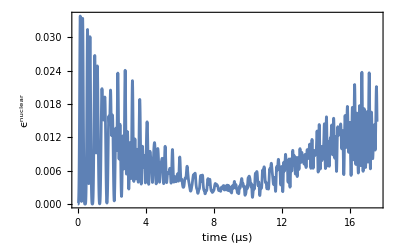

```mathematica
Plot[epsilonCPMGNN[t],{t,0,17.6},Frame-> True,FrameLabel->{"time (μs)","ϵ^nuclear"}, 
LabelStyle->{Directive[Black],40}, PlotRange-> All,FrameStyle->Directive[Black,25]]
```